```mathematica
SetDirectory["/Users/dubard/Documents/Projects/FlexibleNetwork"]
```

/Users/dubard/Documents/Projects/FlexibleNetwork

```mathematica
trainErrorRate = Import["stats/train_error_rate"];
```

Plot::argr: "Plot called with 1 argument; 2 arguments are expected. (*ButtonBox[

```mathematica
testErrorRate = Import["stats/test_error_rate"];
```

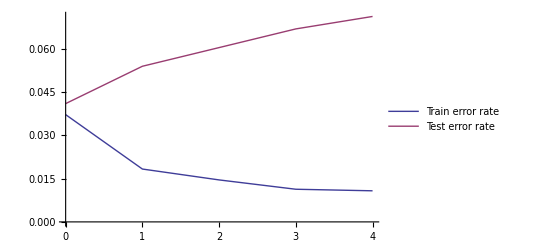

```mathematica
ListLinePlot[{trainErrorRate, testErrorRate}, PlotLegends->{"Train error rate", "Test error rate"}]
```

```mathematica
Export["figs/error_rates.png", %29, ImageResolution->100]
```

fig.png

```mathematica
Import["figs/error_rates.png"]
```

-Graphics-